## PlayPosit1: Sequences

### Q1:

```mathematica
F[n_]:=n^2+n;
```

```mathematica
For[i=1,i<11,i++,Print[F[i]]]
```

2

6

12

20

30

42

56

72

90

Answer = 110

### Q2:

```mathematica
ClearAll[F];
```

```mathematica
F[n_]:=n!
```

```mathematica
InverseFunction[F]
```

F^(-1)

```mathematica
(F^(-1))[5040]
```

7

### Q3:

```mathematica
100!/99! = (100* 99 * 98 * ...)/(99*98*97)=100
```

```mathematica
100!/99!
```

100

### Q4:

```mathematica
∑_(n=1)^3 5n
```

30

## Playposit2: Graphing Polar Curves ft JMT

```mathematica
r=3*Cos[2(θ)]
```

3 Cos[2 θ]

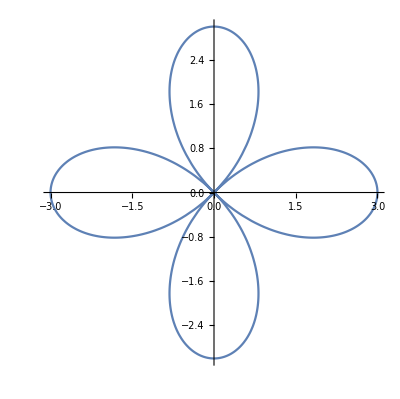

```mathematica
PolarPlot[r,{θ,0,2π}]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
r=√(y^2+x^2);
```

```mathematica
θ=ArcTan[x/y];
```

```mathematica
PolarPlot[Point[{-1,3 π/4}],{θ,0,2π}]
```

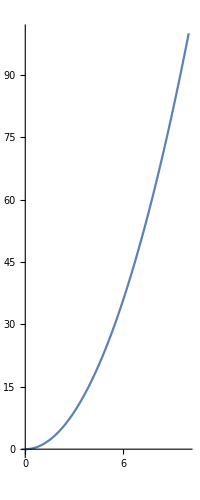

```mathematica
ParametricPlot[{x=t,y=t^2},{t,0,10}]
```

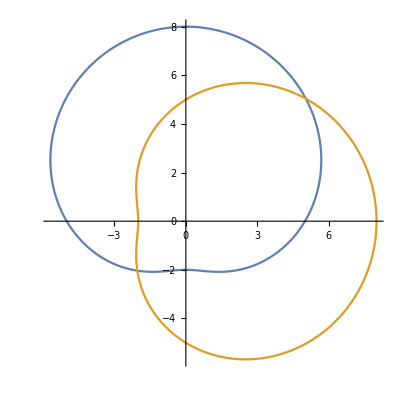

```mathematica
PolarPlot[{r=5+3Sin[θ],r=5+3Cos[θ]},{θ,0,2π}]
```

```mathematica
Solve[5+3Sin[θ]==5+3Cos[θ],θ]
```

{{θ→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[π/4+2 π C[1],C[1]∈ℤ]}}

```mathematica
Together[-(3 π)/4+2 π ]
```

```mathematica
N[(5 π)/4]
```

3.92699

```mathematica
Together[π/4+2 π ]
```

```mathematica
N[(9 π)/4]
```

7.06858

```mathematica
1/2*∫_(5 π/4)^(9 π/4) (5+3Sin[θ])^2 ⅆθ
```

1/2 (-30 √2+(59 π)/2)